Evolution of plant height in crops

Baseline plant fecundity

In the absence of competition, each plant has a baseline fecundity  and produces a random, Poisson distributed, number of seeds  P(fBase[x,xopt]) which is a function of focal plant height, x . We assume that there is an optimal height, xopt (x̂ in the manuscript) , that maximizes baseline fecundity, and fecundity then decreases until zero when plant height is higher than 2 xopt.

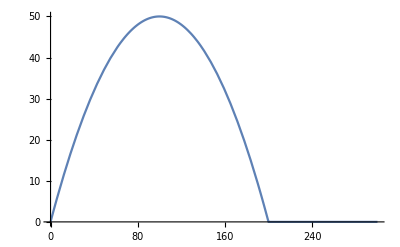

```mathematica
xopt= .; 
fBase[x_,xopt_] := If[x≤2xopt, x(1-x/(2xopt)),0]; 
Plot[fBase[x,xopt] /.{xopt-> 100} , {x,0,300}]
```

# Competition for light

The crop in grown in nF fields. Within fields, plants compete for light with neighboring plants. Fields are composed of nP plants, spaced with distance d. Each plant is represented as an isosceles triangle of height x and angle a at the summit. Plants are competing for light as soon as their respective triangles overlap. For simplicity, we assumed that plants only compete with their two closest neighbors. Then, a focal plant of height x  that competes with neighbors of height yl on the left and yr on the right will have an expected fecundity f[x,xopt,a, yL,yR,d] computed as following:

```mathematica
a = .; (* a is the angle at the summit of isoceles triangles *)
d = .; (* d is the distance between plants *)
cost[x_,a_,yl_,yr_,d_] := 1-If[yl>(d/Tan[a]+x) || yr> (d/Tan[a]+x) ,0,If[yl≤(d/Tan[a]-x) && yr > (d/Tan[a]-x),(Tan[a]*x^2-((Tan[a]*(x+yr)-d)^2)/(4*Tan[a]))/(Tan[a]*x^2),If[yl> (d/Tan[a]-x) && yr ≤ (d/Tan[a]-x),(Tan[a]*x^2-((Tan[a]*(x+yl)-d)^2)/(4*Tan[a]))/(Tan[a]*x^2),If[yl>(d/Tan[a]-x) && yr> (d/Tan[a]-x) && (yl+yr)*Tan[a] ≤ (2*d),(Tan[a]*x^2-(((Tan[a]*(x+yr)-d)^2)/(4*Tan[a]))-(((Tan[a]*(x+yl)-d)^2)/(4*Tan[a])))/(Tan[a]*x^2),If[ yl>(d/Tan[a]-x) && yr> (d/Tan[a]-x) && (yl+yr)*Tan[a] > (2*d),(Tan[a]*x^2-(((Tan[a]*(x+yr)-d)^2)/(4*Tan[a]))-(((Tan[a]*(x+yl)-d)^2)/(4*Tan[a]))+(((Tan[a]*(yl+yr)-2*d)^2)/(4*Tan[a])))/(Tan[a]*x^2),1]]]]];
f[x_,xopt_,a_,yl_,yr_,d_]:= fBase[x,xopt]*(1-cost[x,a,yl,yr,d]);
Manipulate[Plot3D[f[x,xopt,a,yl,yr,d]//.{xopt-> 100, a -> Pi/50, yl-> y, yr-> y}, {x,0,200},{y,0,200},PlotRange->All, AxesLabel-> {"x","y","fecundity"}],{d,1,100}]
```

Productivity per unit area

In a monomorphic population where the phenotype of all individuals is equal to z , the productivity per unit area, or grain yield, is measured by f[z,xopt,a,z,z,d]/d:

```mathematica
ContourPlot[f[x,xopt,a,yl,yr,d]/d //.{xopt->100,a-> Pi/50, x-> z, yl-> z, yr-> z}, { d,.0.01,15},{z,0,200}, FrameLabel->{"d","z"},PlotLegends->Automatic, ColorFunction->ColorData["TemperatureMap"], Contours->100]
```

-Graphics-

Migration

Fields are sown with seeds harvested in the previous season. To sow each field, a fraction (1-m) of the nP  seeds are sampled in the harvest of that field, with  m the seed migration rate. The remaining harvests of all fields are then mixed together and constitute a migrant seed pool. The remaining  m * nP seeds needed for sowing are then sampled in the migrant seed pool for each field. We imagined three seed sampling scenarios based on different modality of migration. In the Within-Fields (WF) scenario, m = 0 : fields are sown with seeds exclusively sampled in their own harvest. In contrast, in the Among-Fields scenario (AF), m  = 1 : fields are sown with seeds exclusively sampled in the migrant seed pool. We introduce parameter α to modulate the contribution of the fields to the migrant seed pool. The case α  = 0  corresponds to the AF scenario: all the fields contribute to the migrant seed pool proportionally to their productivity. When α increases, the probability to pick seeds from the most productive field is magnified. In the third scenario, Top-Field (TF), m = 1 and α tends toward infinity: fields are sown with seeds exclusively sampled in the harvest of the most productive field.

Fitness

We want to derive the fitness function of a focal individual in the meta-population of nF fields. The fitness of a focal plant measures its expected number of adult progenies in the next season. This fitness w[x,y,z]  is a function of x , the focal plant height, y the mean height of the (nP-1)  neighbors of the focal plant, and z the mean height of (nP(nF-1))the  plants in the remaining fields. The fitness function is the sum of the expected number of philopatric offspring (those growing in the field of the focal individual in the next season) and migrant offspring (note, however, that after random dispersal among fields, migrants have a probability  to go back to the field of the focal individual).

Finite number of fields nF

```mathematica
nF= . ; (*nb of fields*) 
nP = .; (* nb of plants per field)*)
m= . ; (* migration rate *)  
α= . ; (* intensity of group selection *)

(* Preliminary functions *)
fec[x_,y_]:= f[x,xopt,a,y,y,d];  (* we re-define the fecundity function to get rid of parameters that are not involved in the derivation of the selection gradient*) 
yR[x_,y_]:=1/nP x+(nP-1)/nP y; (* Resident phenotype: mean plant height in the field of the focal individual(including the focal individual)*)
B[y_,z_]:=Exp[α*fec[y,y]]/Exp[α*fec[z,z]]; (* function that use α to magnify the intensity of group selection. y is the mean phenotype in a given field and z is the mean phenotype in all other (nF-1) fields *)

(* FITNESS *)
W[x_,y_,z_]:=(1-m) Wphilo[x,y,z]+m Wallo[x,y,z];

(* PHILOPATRIC COMPONENT *)
Wphilo[x_,y_,z_]:=fec[x,y]/(CompPhiloR[x,y]+CompImmig[x,y,z]);

CompPhiloR[x_,y_]:=(1-m)fec[yR[x,y],yR[x,y]];
CompImmig[x_,y_,z_]:=m(1/nF B[yR[x,y],z]fec[yR[x,y],yR[x,y]]+(nF-1)/nF B[z,z]fec[z,z]);

(* ALLOPATRIC COMPONENT *)
(* Seeds of the focal plant can return to their parental field with probability 1/nF. In this case,they compete with both phylopatric seeds from the parental field and immigrant seeds. With probability (nF-1)/nF, seeds migrate to a different field where they compete with the local phylopatric seeds and the immigrand seeds*)
Wallo[x_,y_,z_]:=1/nF((fec[x,y]B[yR[x,y],z])/(CompPhiloR[x,y]+CompImmig[x,y,z]))+(nF-1)/nF((fec[x,y]B[yR[x,y],z])/(CompPhiloI[z]+CompImmig[x,y,z]));

(* si les graines dispersantes se retrouvent dans pop différente de l'origine *)
CompPhiloI[z_]:=(1-m)fec[z,z]
```

Approximate fitness function when nF and nP >> 0

When nF >> 0, terms with 1/nFbecome negligible compared to terms with (nF-1)/nF, and the same is true when nP >> 0 for terms with 1/nP  and (nP-1)/nP. This simplifies the CompImmig function and the Wallo function. Note also that B[z,z] = 1

```mathematica
Ws[x_, y_, z_]:=(1-m) fec[x,y]/((1-m)fec[y, y]+ m fec[z,z]) + m (B[y,z]fec[x,y])/fec[z,z];
```

Relatedness

R (relatedness) depends upon multiple factors such as seed sampling rules and crop reproductive biology. We compute R under the following assumptions. Individuals are haploid and reproduce asexually. Plant height is determined by a single locus. Progenies can differ in height from their parent with probability μ, the mutation rate. We further assume that the farmer draws a number of founding seeds, nS, in the harvest, which are multiplied before sowing. In the finite island model, relatedness can be expressed as follows (Rousset and Billiard 2000): R = (Q_0 - Q_1)/(1 - Q_1) 

where Q_0  is the probability that two plants within a field have identical alleles for plant height and Q_1 the probability that two plants from different fields share the same allele for plant height. Following Cockerham and Weir (1987), we define the two following probabilities:

```mathematica
μ = .; (* the mutation rate *)
γ = . ;(*probability that none of the two sampled seeds mutated away from the parental genotype: γ = (1-μ)^2*)
nS= .; (*number of seeds sampled to repopulate each field*)
ϕ = .; (* controls the probability that two founding seeds sampled in the migrant seed pool originate from the same field *)

Pw=(1-m)^2+m^2(ϕ+(1-ϕ)/nF) ;
Pa=(2m(1-m))/nF+m^2(ϕ+(1-ϕ)/nF);
```

with  Pw the probability that two founding seeds of a field at time t were produced in the same field at time t-1 and Pa the probability that two founding seeds of distinct fields at time t were produced in the same field at time t-1. The parameter ϕ  controls the probability that two founding seeds sampled in the migrant seed pool originate from the same field. When α, the parameter that scales the magnitude of among-field competition (see above) equals zero, then ϕ = 0. In that case, fields contribute to the migrant seed pool proportionally to their productivity (scenario AF), and the probability of sampling two seeds in the migrant seed pool that originate from the same field is 1/nF. In contrast, when α tends toward infinity, ϕ = 1. In that case, all the seeds in the seed pool originate from the most productive field (scenario TF). Then, we can write Q0 and Q1 probabilities at t as a function of Q_0 and Q_1 probabilities at t-1, respectively Q_0’ and Q_1’:

Q0=γ(1/nS+(nS-1)/nS(Pw(1/nP+(nP-1)/nP Q0')+(1-Pw)Q1'))
Q1=γ(Pa(1/nP+(nP-1)/nP Q0')+(1-Pa)Q1'))

Solving the equation system

```mathematica
{Qw,Qb}=First[{Q0,Q1}/.FullSimplify[Solve [Q0==γ(1/nS+(nS-1)/nS(Pw(1/nP+(nP-1)/nP Q0)+(1-Pw)Q1))&&Q1==γ(Pa(1/nP+(nP-1)/nP Q0)+(1-Pa)Q1),{Q0,Q1}]]]
```

{(γ (-nF (-1+nP+nS) (-1+γ)+2 m (nF (-1+nS) (-1+γ)+(-1+nP+nS) γ)+m^2 (-1-nF+nS+nF nS+2 γ+nF γ-nP γ-2 nS γ-nF nS γ+(-1+nF) (-1+nS+nP γ) ϕ)))/(nF ((-1+γ) (-nP nS+(-1+m)^2 (-1+nP) (-1+nS) γ)+m^2 (-1+nP+nS) γ ϕ)+m γ (2 nP nS-2 (-1+nP) (-1+nS) γ+m nP (1+2 nS (-1+γ)-2 γ-ϕ)-m (-1+nS) (-1+2 γ+ϕ))),(m γ (nS+(-1+nP) γ) (2+m (-1+(-1+nF) ϕ)))/(nF ((-1+γ) (-nP nS+(-1+m)^2 (-1+nP) (-1+nS) γ)+m^2 (-1+nP+nS) γ ϕ)+m γ (2 nP nS-2 (-1+nP) (-1+nS) γ+m nP (1+2 nS (-1+γ)-2 γ-ϕ)-m (-1+nS) (-1+2 γ+ϕ)))}

Defining relatedness with the solutions:

```mathematica
FullSimplify[(Qw-Qb)/(1-Qb)]
```

(γ (nF-nF (nP+nS)+2 m (nF (-1+nS)+nS)+m^2 (1+nF-2 nS-nF nS+(-1+nF) ϕ)))/(m (-1+nP) γ (-2 nS+m (-1+2 nS+ϕ))+nF (-(-1+m)^2 (-1+nS) γ+nP nS (-1+(-1+m)^2 γ)+m^2 γ ϕ-nP γ (1+m (-2+m+m ϕ))))

```mathematica
Relatedness[nF_, nP_, nS_, m_, γ_, ϕ_]:=(γ (nF-nF (nP+nS)+2 m (nF (-1+nS)+nS)+m^2 (1+nF-2 nS-nF nS+(-1+nF) ϕ)))/(m (-1+nP) γ (-2 nS+m (-1+2 nS+ϕ))+nF (-(-1+m)^2 (-1+nS) γ+nP nS (-1+(-1+m)^2 γ)+m^2 γ ϕ-nP γ (1+m (-2+m+m ϕ))));
```

Simplifying the expression of relatedness when both nF and nP are large:

```mathematica
FullSimplify[Normal[Series[Relatedness[nF,nP,nS,m,γ,ϕ],{nF,Infinity,0},{nP,Infinity,0}]]]
```

-γ/(nS (-1+(-1+m)^2 γ)-γ (1+m (-2+m+m ϕ)))

```mathematica
R[nS_, m_, γ_, ϕ_]:=-γ/(nS (-1+(-1+m)^2 γ)-γ (1+m (-2+m+m ϕ)));
Manipulate[
Plot[{R[nS, m, γ, ϕ],Relatedness[nF,nP,nS,m,γ,ϕ]},{nS,1,30},PlotRange->{0,1},PlotStyle->{Black, Red},AxesLabel->{"NB of FOUNDING SEEDS","RELATEDNESS"}],{m,0.01,1},{nP,10,1000},{nF,2,20},{γ,0.9,1},{ϕ,0,1}]
```

## Selection Gradient

The selection gradient can be computed from the fitness function under the assumption that selection is weak (Taylor and Frank 1996; Rousset and Billiard 2000): ∆S =  (∂w)/(∂x)+R(∂w)/(∂y)
where all the derivatives are evaluated at x = y = z  and where  R is relatedness (see above for a derivation of the equilibrium value of relatedness). Singular strategies correspond to strategies where the gradient of selection  equals to zero.

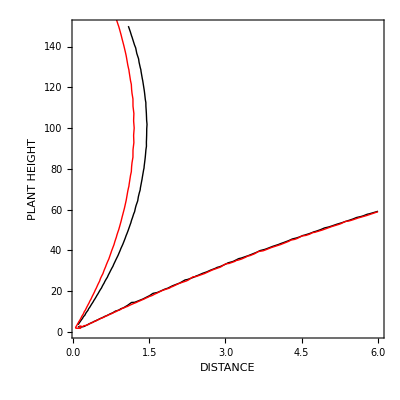

```mathematica
(* complete fitness functions and complete relatedness function *)S1 = ContourPlot[D[W[x, y, z],x]+Relatedness[nF, nP, nS, m, γ, ϕ]*D[W[x, y, z],y]//.{xopt-> 100, a-> Pi/50, α -> 0, m-> 1, nF-> 20, nP-> 200,nS-> 1, m-> 1, γ-> 0.81, ϕ -> 0, x-> z, y-> z}, {d, 0.1, 6}, {z, 0,150},Contours-> {0}, FrameLabel->{"DISTANCE", "PLANT HEIGHT"}, ContourShading->None,ContourStyle->Black ];(* simplified fitness functions and simplified relatedness function *) 
S2 = ContourPlot[D[Ws[x, y, z],x]+R[nS, m, γ, ϕ]*D[Ws[x, y, z],y]//.{xopt-> 100, a-> Pi/50, α -> 0, m-> 1, nF-> 20, nP-> 200,nS-> 1,γ-> 0.81, ϕ -> 0, x-> z, y-> z}, {d, 0.01,6}, {z, 0,200},Contours-> {0}, FrameLabel->{"DISTANCE", "PLANT HEIGHT"}, ContourShading->None,ContourStyle->Red];
Show[S1, S2]
```